# Values for τα

## scattering function

## N=4096

```mathematica
test=Import["/home/chengling/Research/Project/Cell/glassAging/fluidConfigurations/scatteringFunction_N4096_TEq0.10000000_p3.80000_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
plist={3.75, 3.8 ,3.825 ,3.85, 3.9, 4.0};
pstring=ToString[NumberForm[#,{9,5},ExponentFunction->(Null&)]]&/@plist
```

{3.75000,3.80000,3.82500,3.85000,3.90000,4.00000}

```mathematica
sk4096=Table[Table[Import["/home/chengling/Research/Project/Cell/glassAging/fluidConfigurations/scatteringFunction_N4096_TEq0.10000000_p"<>pstring[[p]]<>"_idx"<>ToString[id]<>".nc","Data"],{id,0,19}],{p,Length[plist]}];
```

```mathematica
Normal[sk4096[[5,15,2,1]]]
```

0.0134008

```mathematica
0.14726215563702155
```

```mathematica
0.14726215563702155
```

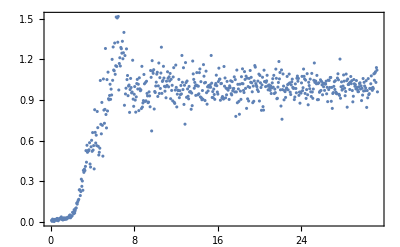

```mathematica
ListPlot[Table[{test[[1,i]],test[[2,i]]},{i,Length[test[[1]]]}]]
```

```mathematica
sk=Table[Table[{sk4096[[p,1,1]][[t]],Mean[Table[sk4096[[p,id,2]][[t]],{id,20}]]},{t,Length[sk4096[[p,1,1]]]}],{p,Length[plist]}];
```

```mathematica
sk[[3,110]]
```

{5.49779,0.951295}

```mathematica
Table[ListPlot[Table[{sk4096[[p,1,1]][[t]],Mean[Table[sk4096[[p,id,2]][[t]],{id,20}]]},{t,Length[sk4096[[p,1,1]]]}],PlotStyle->redBluePlotConfig[6][[7-p]],PlotLegends->StringJoin["p=",ToString[plist[[p]]]],FrameLabel->{"k","S(k)"},ImageSize->600,PlotMarkers->Automatic,PlotRange->{{0,10},All},Joined->True],{p,Length[plist]}]
```

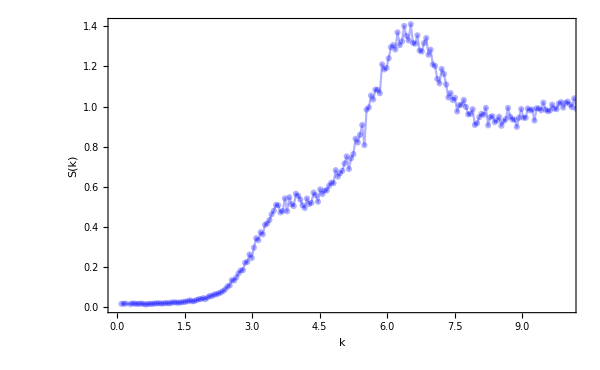
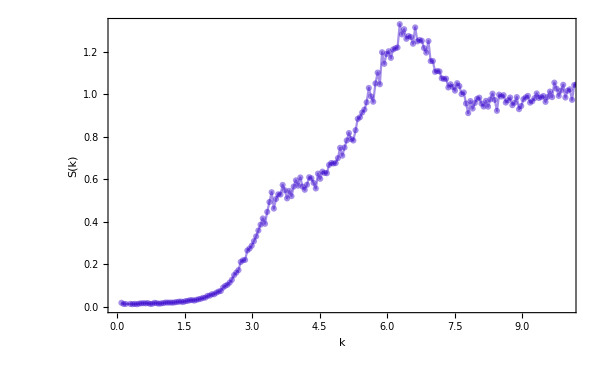
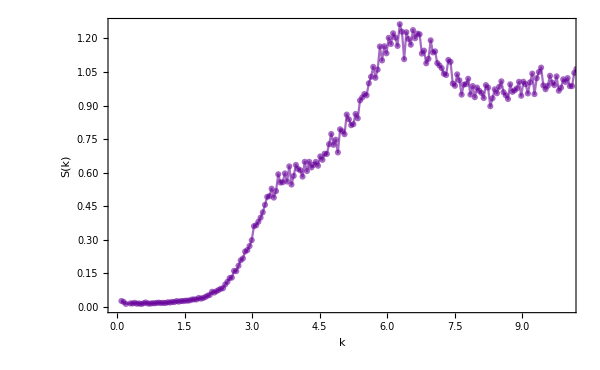
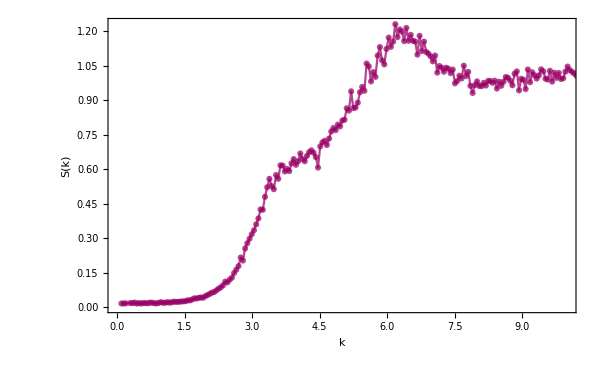
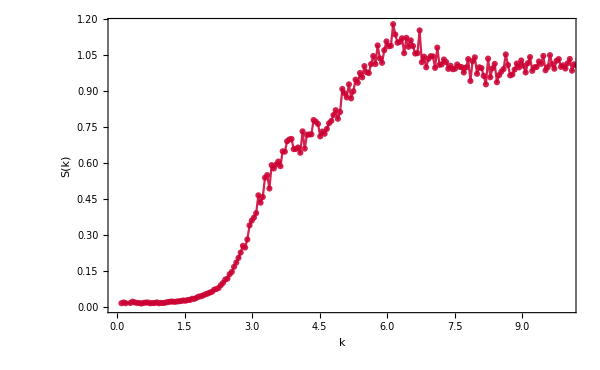
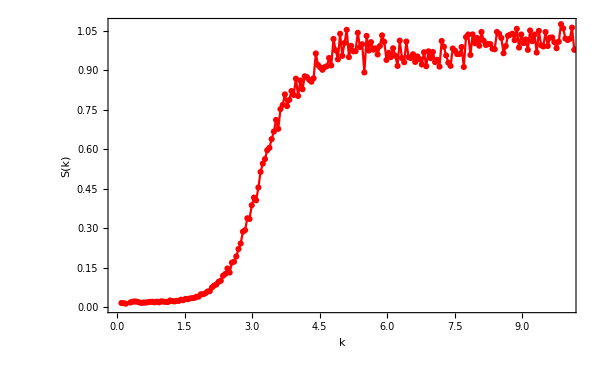

```mathematica
klist={6.55,6.50,6.40,6.35,6.30,5.35};
```